# Derivation of p(x|I_1) for J=2

```mathematica
J=n=2;
```

```mathematica
Solve[r==Log[x/c]&&s==Log[y/x]&&0<c<x≤y,{x,y},PositiveReals]//FullSimplify
a={c ⅇ^r,c ⅇ^(r+s) };
b={r,s};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&r>0&&s>0],y→ConditionalExpression[c ⅇ^(r+s),c>0&&r>0&&s>0]}}

c^2 ⅇ^(2 r+s)

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]]
m[{r,s}]
```

ⅇ^s

```mathematica
Z[λ_]:=Integrate[m[{r,s}] Exp[-{r,s}.λ],{r,0,∞},{s,0,∞},Assumptions->λ∈Vectors[2,Reals]&&ρ>0]//FullSimplify
Z[{ρ,σ}]
```

1/(ρ (-1+σ))

```mathematica
(* Show that ρ is indeed positive, as we assumed in the integral *)
Assuming[ρ>0,D[Log[Z[{ρ,σ}]],{{ρ,σ},1}]==-{mr,ms}]
MEsolution=Solve[%,{mr,ms}][[1]]
```

{-1/ρ,-1/(-1+σ)}=={-mr,-ms}

{mr→1/ρ,ms→1/(-1+σ)}

The canonical ME solutions show the (current) constraints on the Lagrange multipliers: ρ>0,σ>1.

```mathematica
p[u_,λ_]:=(1/Z[λ]) m[u] Exp[-u.λ] (*Boole[AllTrue[u,0<#&]]*)
p[{r,s},{ρ,σ}]
```

ⅇ^(s-r ρ-s σ) ρ (-1+σ)

```mathematica
Integrate[p[{r,s},{ρ,σ}],{r,0,∞},{s,0,∞},Assumptions->ρ>0]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,y_,c_,ρ_,σ_]:=p[{Log[x/c],Log[y/x]},{ρ,σ}]/(x y) Boole[0<c≤x≤y]
q[x,y,c,ρ,σ]//FullSimplify
```

Piecewise[{{c^ρ x^(-2-ρ+σ) y^-σ ρ (-1+σ), c>0&&c≤x&&x≤y}, {0, True}}]

```mathematica
Integrate[q[x,y,c,ρ,σ],{x,-∞,∞},{y,-∞,∞},Assumptions->0<c&&ρ>0]
```

1

Use the constraints on the Lagrange multipliers derived above to drastically improve MMA's performance on these integrals.

```mathematica
px[x_,c_,ρ_,σ_]=Integrate[q[x,y,c,ρ,σ],{y,-∞,∞},Assumptions->0<c&&ρ>0&&σ>1]
py[y_,c_,ρ_,σ_]=Integrate[q[x,y,c,ρ,σ],{x,-∞,∞},Assumptions->0<c&&ρ>0&&σ>1]
```

Piecewise[{{c^ρ x^(-1-ρ) ρ, c>0&&c-x≤0}, {0, True}}]

Piecewise[{{-(y^(-1-ρ-σ) (-c^σ y^(1+ρ)+c^(1+ρ) y^σ) ρ (-1+σ))/(c (1+ρ-σ)), c>0&&c-y<0}, {0, True}}]

For the moments of x,y to exist, the requirements on the Lagrange multipliers are stricter: ρ>0,σ>1 now becomes ρ>1,σ>2.

```mathematica
Ex=Integrate[x px[x,c,ρ,σ],{x,-∞,∞},Assumptions->0<c&&ρ>1&&σ>2]//FullSimplify
Ey=Integrate[y py[y,c,ρ,σ],{y,-∞,∞},Assumptions->0<c&&ρ>1&&σ>2]//FullSimplify
```

(c ρ)/(-1+ρ)

(c ρ (-1+σ))/((-1+ρ) (-2+σ))

## Solve for Lagrange multipliers given formant frequency first moments

It is seen that the solutions automatically enforce the constraints on the Lagrange multipliers that allowed the moments to exist in the first place. This is logical: since we assert the first moments, our ME distribution better allows them to exist. Since these enforced constraints are stricter than those implied by the ME solutions in terms of first moments of u and those necessary for Z(λ) to exist, everything is well-defined.

```mathematica
mcond=0<c<mF1<mF2;
```

```mathematica
sol=Refine[Solve[mF1==Ex&&mF2==Ey&&mcond&&ρ>1&&σ>2,{ρ,σ},Reals],Assumptions->mcond][[1]]//FullSimplify
```

{ρ→mF1/(-c+mF1),σ→2+mF1/(-mF1+mF2)}

## Plots

Marginals p(x_i|c,μ_(1:i)) are identical for any n≥i given the same information c,μ_(1:i). So indeed knowledge of higher formants does not influence the marginals of lower formant frequencies.

```mathematica
marginals={px[x,c,ρ,σ],py[y,c,ρ,σ]}/.{y->x}/.sol/.{c->200,mF1->500,mF2->1000}//N//FullSimplify
```

{Piecewise[{{0., x<200.}, {11399.8/x^(8/3), True}}],Piecewise[{{0., x≤200.}, {(-400000.+68399. x^(1/3))/x^3, True}}]}

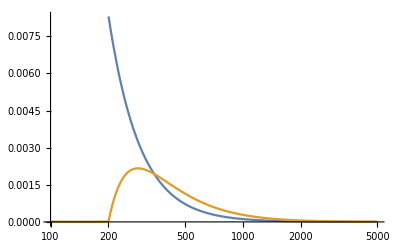

```mathematica
LogLinearPlot[marginals,{x,100,5000},PlotRange->Full]
```